# Matemáticas CA 3

Prof: Roberto Méndez Méndez

Funciones

```mathematica
f[x_,y_]:= x + 4*y*y 
Plot3D[f[x,y] , {x, -5, 5}, {y, -1, 1}, AxesLabel->{x,y,z}]
```

-Graphics3D-

## Funciones Paramétricas

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t},{t,0,4π}]
```

-Graphics3D-

Excercise 15 Thomas pág  373

```mathematica
ContourPlot3D[{y^2+z^2==1, x^2+z^2==1},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
ContourPlot3D[{y^2+z^2==1, x^2+z^2==1},{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-

```mathematica
ContourPlot3D[{y^2+z^2==1, x^2+z^2==1},{x,-1,1},{y,-1,1},{z,0,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x, Sin[x],Cos[x]},{x, 0, 4*Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x, x,Sqrt[1 - x^2]},{x, -1, 1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{x, x,Sqrt[1 - x^2]}, {x, -x,Sqrt[1 - x^2]} },{x, -1, 1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sqrt[1 - z^2], Sqrt[1 - z^2],z},{z, 0, 1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{Sqrt[1 - z^2], Sqrt[1 - z^2],z}, {-Sqrt[1 - z^2], -Sqrt[1 - z^2],z} },{z, 0, 1}]
```

-Graphics3D-

### Vector Field

```mathematica
a = 100000
G = 6.674*10^(-11);
M = 5.972*10^(24);
m = 1000;
r = {200, 344, 500};
F = (m*M*G)/Norm[r]^3*r
VectorPlot3D[-(m*M*G)/Norm[{x,y,z}]^3* {x,y,z}, {x,-a,a},{y,-a,a}, {z,-a,a}]
```

100000

{3.05499×10^11,5.25458×10^11,7.63747×10^11}

-Graphics3D-

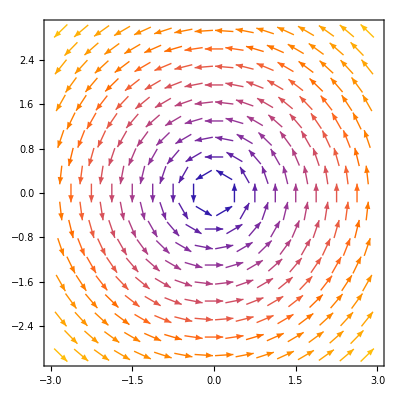

```mathematica
VectorPlot[{-y,x},{x,-3,3},{y,-3,3}]
```

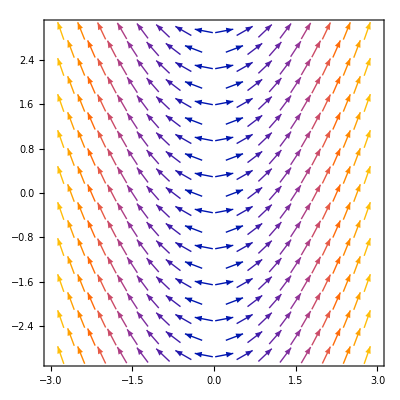

```mathematica
vpFxxx = VectorPlot[{x,x^2},{x,-3,3},{y,-3,3}]
```

### Conservative vector Field

Gravitational field is a conservative field
Note: this first form isn’t  as expected,

```mathematica
Grad[(m*M*G)/Norm[{x,y,z}], {x,y,z}]
```

{-(3.98571×10^17 Abs[x] Abs'[x])/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),-(3.98571×10^17 Abs[y] Abs'[y])/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),-(3.98571×10^17 Abs[z] Abs'[z])/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

```mathematica
Grad[1/(√(x^2+ z^2 + y^2)), {x,y,z}]
```

{-x/((x^2+y^2+z^2)^(3/2)),-y/((x^2+y^2+z^2)^(3/2)),-z/((x^2+y^2+z^2)^(3/2))}

```mathematica
Grad[(m*M*G)/(√(x^2+ z^2 + y^2)), {x,y,z}]
```

{-(3.98571×10^17 x)/((x^2+y^2+z^2)^(3/2)),-(3.98571×10^17 y)/((x^2+y^2+z^2)^(3/2)),-(3.98571×10^17 z)/((x^2+y^2+z^2)^(3/2))}

#### Streamlines

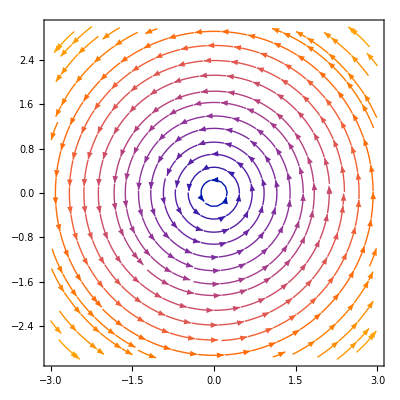

```mathematica
StreamPlot[{-y,x},{x,-3,3},{y,-3,3}]
```

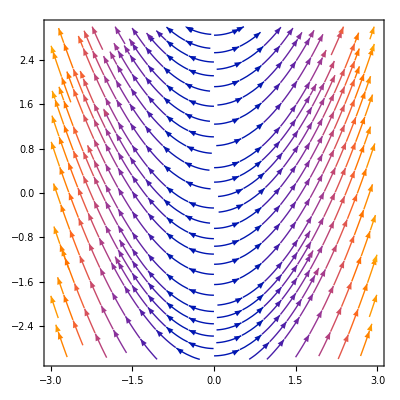

```mathematica
StreamPlot[{x,x^2},{x,-3,3},{y,-3,3}]
```

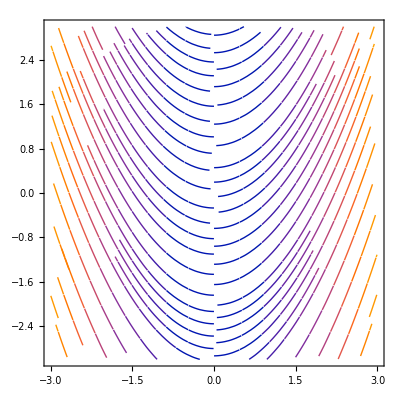

```mathematica
spFxxx =StreamPlot[{x,x^2},{x,-3,3},{y,-3,3}, StreamMarkers-> None]
```

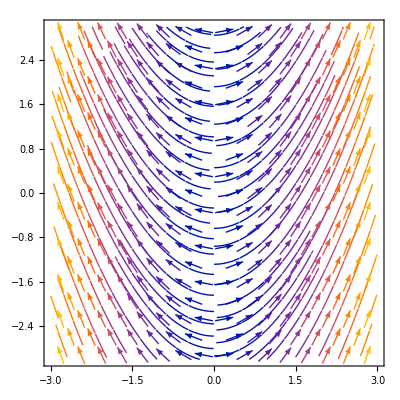

```mathematica
Show[vpFxxx, spFxxx]
```

### Area with double integral

```mathematica
f[x_, y_] := 1 -y
Plot3D[f[x,y],{x,0,1},{y,0,1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
∫_0^1 ∫_0^1 (1-y)ⅆxⅆy
```

1/2

```mathematica
f[x_, y_] := x^2 -y^2   + 1
Plot3D[{f[x,y],0},{x,-1,1},{y,-1,1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
∫_-1^1 ∫_-1^1 f[x,y]ⅆxⅆy
∫_-1^1 ∫_-1^1 (f[x,y]- 1)ⅆxⅆy
```

4

0

```mathematica
f[x_, y_] := x^2 -y^2  
Plot3D[{f[x,y],0},{x,-1,1},{y,-1,1}, AxesLabel->Automatic]
```

-Graphics3D-